# Nodes have a limited capacity, only a subset of nodes deliver packages.

```mathematica
NotebookDirectory[]
```

/home/jovillal/git/redes/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jovillal/git/redes

```mathematica
$HistoryLength=5;
```

Represent a graph as a list of it nodes, each node a list {m_j,{n_j1,n_j2,…,n_jN_j}}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,…,n_jN} the list of neighbors of node m.
When ω_(j k)==0 or Sin[ω_(j k) t+ϕ_(j k)]≥ 0 marbles can leave the node, here ω_(j k) is a frequency, and ϕ_(j k) is a phase associated to the link that connects nodes j and k.
All nodes have a fixed capacity K, no node may have more than K packages at a given time (not implemented yet).
Given a network, the rules of the simulation are that at every tick:
	■ A subset of nodes P is selected according to weights m^α, where m={m_i} is the number of packages in node i. 
	◼ Every node in the subset tries to pass one of its marbles to one of its neighbors (chosen randomly). 
	■ A marble is passed if ω_(j k)==0∨Sin[ω_(j k) t+ϕ_(j k)]≥ 0, otherwise the marble stays. 
	■ A node receives all incoming marbles if its capacity is not exceeded.

## Functions

## Auxiliaries

eCR[m, i,j] takes a matrix m and exchanges columns and rows i and j.

```mathematica
eCR[am_?MatrixQ,column_Integer,row_Integer]:=Block[{ret=am},
ret[[{column,row}]]=ret[[{row,column}]];
{ret[[All,column]],ret[[All,row]]}={ret[[All,row]],ret[[All,column]]};
ret]
```

sortByOut[m] takes an adjacency matrix and sorts it in a way that VertexOutDegree[AdjacencyGrapg[sortByOut[m]]] is sorted from greater to less, this is equivalent to saying that the first node has the highest out degree and the last node has the smallest.

```mathematica
sortByOut[am_?MatrixQ/;Length[am]==Length[Transpose[am]]]:=Module[
{out=Total/@am,new=am,i,ex},
Do[
If[out[[i]]<Max[out[[i+1;;-1]]],
new=eCR[new,i,i+FirstPosition[out[[i+1;;-1]],Max[out[[i+1;;-1]]]][[1]]];
out=Total/@new;]
,{i,Length[am]-1}];
new
];
sortByOut[_]:=Print["sortByOut input is not a matrix or a square matrix."]
```

sortByIn[m] takes an adjacency matrix and sorts it in a way that VertexInDegree[AdjacencyGrapg[sortByIn[m]]] is sorted from greater to less, this is equivalent to saying that the first node has the highest in degree and the last node has the smallest.

```mathematica
sortByIn[am_?MatrixQ/;Length[am]==Length[Transpose[am]]]:=Module[
{in=Total/@Transpose[am],new=am,i,ex},
Do[
If[in[[i]]<Max[in[[i+1;;-1]]],
new=eCR[new,i,i+FirstPosition[in[[i+1;;-1]],Max[in[[i+1;;-1]]]][[1]]];
in=Total/@Transpose[new];]
,{i,Length[am]-1}];
new
];
sortByIn[_]:=Print["sortByIn input is not a matrix or a square matrix."]
```

remove[g,P] takes a graph g as  defined by graphToNet and an integer P that gives the number of nodes that are supposed to donate one marble.
It returns a set of pairs {i,b_i} where b_i=0 if node i can’t donate or b_i∈{M} indicates the receiving node.

```mathematica
remove[g_,P_Integer/;0<P<=M]:=Module[{occ=Length/@g[[All,1]],ret,subset},
If[α==0,Off[Power::indet]];
occ=occ^α;
If[α==0,On[Power::indet];occ=occ/.Indeterminate->0];
(*Print["occ is ",occ];*)
subset=Position[occ,x_/;x>0]//Flatten;
(*Print["subset is ",subset];*)
subset=If[Length[subset]>P,
Sort[RandomSample[occ->Range[M],P]],
Sort[RandomSample[occ->Range[M],Length[subset]]]
];
(*Print["subset is ",subset];*)
Table[If[g[[i,2]]≠{}&&g[[i,1]]!={},{i,RandomChoice[g[[i,2]]]},{i,0}],{i,subset}]
];
```

add[g,out] takes a graph g as  defined by graphToNet, and list of integers out (output from remove). It returns a set of lists {{δ_i,r_i}}  where δ_i is the set of marbles that arrive at node i, and r_i the set of packages that exit node i.

```mathematica
add[g_List,{}]:=ConstantArray[{{},{}},M];
add[g_List,{{_,0}}]:=ConstantArray[{{},{}},M];
add[g_List,out_List/;Length[out]==1]:=Module[{r=ConstantArray[{},M],δ=ConstantArray[{},M]},
(*build the r*)
r=ReplacePart[r,out[[1,1]]->{g[[out[[1,1]],1,1]]}];
(*now build the δ*)
δ=ReplacePart[δ,out[[1,2]]->{g[[out[[1,1]],1,1]]}];
Transpose[{δ,r}]
];
add[g_List,out_List/;out[[2,All]]==ConstantArray[0,Length[out]]]:=ConstantArray[{{},{}},M];
add[g_List,out_List/;Length[out]==M]:=Module[{ct,pct,rem=out,i},
ct=Count[out[[All,2]],#]&/@Range[M] (*Number of packages each node will receive*);
(*Print[ct];*)
(*pct=Table[Boole[RandomReal[]<=prob[Length[graph[[i,1]]],ct[[i]],Tmp]],{i,M}]*)
(*This is 0 or 1 depending on the probability of recieving*);
(*Print[pct];*)
(*pct=ct*pct (*now pct has the accurate number of packages that every node will recieve*);*)
(*Print[pct];*)
(*Modify out with the accurate number of packages*)
(*For[i=1,i<=M,i++,
If[ct[[i]]!=pct[[i]],
rem=ReplacePart[rem,Thread[Rule[Cases[Position[rem,ct[[i]]],{_,2}],0]]]
]
];*)
(*now build the r*)
ct=Table[If[rem[[i,2]]!=0,{g[[i,1]][[1]]},{}],{i,M}];
(*Print["This is r ",ct];*)
(*now build the δ*)
pct=Table[With[{x=Position[rem[[All,2]],i]},
If[x=={},{},
Table[g[[j,1]][[1]],{j,Flatten[x]}]
]],{i,M}];
(*Print["This is δ ",pct];*)
Transpose[{pct,ct}]
];
add[g_List,out_List/;1<Length[out]<M]:=Module[{ct,r,donors,δ=ConstantArray[{},M],i},
ct=Count[out[[All,2]],#]&/@Range[M] (*Number of packages each node will receive*);
donors=Cases[out,{x_,j_/;j>0}->x];
(*Print["This is ct ",ct];
Print["This is donors ",donors];*)
(*now build the r*)
r=Table[If[MemberQ[donors,i],{g[[i,1]][[1]]},{}],{i,M}];
(*Print["This is r ",r];*)
(*now build the δ*)
For[i=1,i<=M,i++,
If[ct[[i]]!=0,
δ[[i]]=Table[g[[out[[j,1]],1,1]],{j,Flatten[Position[out[[All,2]],i]]}]]
];
(*Print["This is δ ",δ];*)
Transpose[{δ,r}]
];
```

updateGraph[g, a] takes a graph g and a list of pairs a={{δ_i,r_i}} (output from add), and returns and updated version of g consistent with a.

```mathematica
updateGraph[g_List,a_List/;a==ConstantArray[{{},{}},M]]:=g;
updateGraph[g_List,a_List]:=Module[{packs=g[[All,1]]},
packs=Table[Drop[packs[[i]],Length[a[[i,2]]]],{i,M}];
packs=Table[Flatten[Append[packs[[i]],a[[i,1]]]],{i,M}];
Transpose[{packs,g[[All,2]]}]
];
```

fillWith[marbles] takes an integer and returns an array of size M with a list of integers m_i at position i, such that ∑_i Length[m_i]==marbles and Length[m_i]≃Length[m_j] for all places.

```mathematica
fillWith[marbles_Integer]:=Module[{int=Floor[marbles/M],float=Mod[marbles,M],ret,count=1},
ret=RandomSample[ConstantArray[int,M]+Join[ConstantArray[1,float],ConstantArray[0,M-float]]];
Table[If[ret[[i]]==0,{},count=count+ret[[i]];Range[count-ret[[i]],count-1]],{i,M}]
]
```

padTally[l, n] takes a list of pairs ordered by the first element and returns a list of length n of the form {{0,p_0},{1,p_1},…,{n-1,p_(n-1)}} where p_i=0 or p_i==l[[j,2]] if l[[j,1]]==i+1.

```mathematica
padTally[l_,n_]:=l/;Length[l]≥n;
padTally[l_,n_]:=Block[{ret},
ret=ReplacePart[ConstantArray[0,n],MapThread[Rule,{l[[All,1]]+1,l[[All,2]]}]];
{Range[n]-1,ret}//Transpose
];
```

spread[r] returns de width of an Around object. It returns 0 otherwise.

```mathematica
spread[x_Around]:=2 x[[2]];
spread[_]:=0;
```

## Main functions

graphToNet[graph, ini,order] takes a graph (Mathematica style) and returns a list of elements {{m_i},{n_(j 1),n_(j 2),…,n_(j N_j)}}; with {m_i} the set of packages in the node, and j∈{1,…, N} (N the number of nodes in the graph), n_(j s) the s-th outer neighbour of node j.  The elements are ordered by default according to their outdegree (the first node has the biggest outdegree).
ini can be one of the following:
	• an integer a, will put a marbles on each node.
	• a list of two integers {a,n}, this would put a marbles on node n and no marbles on the other nodes.
	• a list of integers of length N that represents the initial distribution of marbles
order is optional, it determines the order of the elements according to their the out degree 
	• if order is omitted or order≡"Out"  (or whatever else) elements are ordered according to their outdegree (the first node has the biggest outdegree).
	• if order≡"In"  elements are ordered according to their indegree (the first node has the biggest indegree).

```mathematica
graphToNet[g_Graph,ini_Integer]:=Module[{nei},
nei=sortByOut[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
Transpose[{Partition[Range[ini VertexCount[g]],ini],nei}]
];
graphToNet[g_Graph,ini:{a_,n_}]:=Module[{nei},
nei=sortByOut[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
ReplacePart[{{},#}&/@nei,{n,1}->Range[a]]
];
graphToNet[g_Graph,ini_List]:=Module[{nei},
nei=sortByOut[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
graphToNet[g_Graph,ini:{a_,n_},"Out"]:=graphToNet[g,{a,n}];
graphToNet[g_Graph,ini_List,"Out"]:=graphToNet[g,ini];
graphToNet[g_Graph,ini:{a_,n_},"In"]:=Module[{nei},
nei=sortByIn[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
ReplacePart[{{},#}&/@nei,{n,1}->Range[a]]
];
graphToNet[g_Graph,ini_List,"In"]:=Module[{nei},
nei=sortByIn[Normal[AdjacencyMatrix[g]]];
nei=Flatten[Position[#,1]]&/@nei;
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
```

netEvolve[graph,T] takes a graph (represented as previously described), with M nodes,  and implements the rule described above for T ticks, there is no maximum number of marbles per node. It returns a list E where every element represents the state of the graph at time t. For each time t, there are M elements that contain the marbles present in each node. This is E[[t,m]] gives a list with the marbles present at time t in node m.
This version assumes ω_(j k)=ϕ_(j k)=0

```mathematica
netEvolve[graph_List,T_Integer]:=NestList[updateGraph[#,add[#,remove[#,M]]]&,graph,T]
```

netEvolve[graph,P,T] takes a graph (represented as previously described), with N nodes, and two integers 1<=P<N and T, and implements the rule described above for T ticks. P defines the number of nodes that deliver one package per tick. It returns a list E where every element represents the state of the graph at time t. For each time t, there are N elements that contain the marbles present in each node. This is E[[t,m]] gives a list with the marbles present at time t in node m.
This version assumes ω_(j k)=ϕ_(j k)=0

```mathematica
netEvolve[graph_List,M,T_Integer]:=netEvolve[graph,T];
netEvolve[graph_List,P_Integer/;1<=P<M,T_Integer]:=Module[{subset},
NestList[updateGraph[#,add[#,remove[#,P]]]&,graph,T]
]
```

difCoef[mrb, evol, net] takes a group of marbles mrb, the evolution of a network evol (as produced by netEvol), and a network net (as produced by  graphToNet) and calculates the diffusion coefficient for each pair of marbles in mrb. It returns a linear model for each par of coefficients, assuming that, once on a relaxed state, two marbles in the same node drift apart ∝β t^h (the linear model is of the form h x).

```mathematica
difCoef[{m1_Int}|{},evol_List,net_List]:={};
difCoef[pairs:{m1_Int,m2_Int_},evol_List,net_List]:=Module[{distances},
distances=distanceBetween[pairs,evol,net];
LinearModelFit[Transpose[{Log[Range[2,Length[#]]],Log[Rest[#]+1]}],x,x,IncludeConstantBasis->False]&/@distances
];
difCoef[mrb_List,evol_List,net_List]:=Module[{distances,pairs=Cases[Permutations[mrb,{2}],{x_,y_}/;x<y]},
distances=distanceBetween[#,evol,net]&/@pairs;
LinearModelFit[Transpose[{Log[Range[2,Length[#]]],Log[Rest[#]+1]}],x,x,IncludeConstantBasis->False]&/@distances
];
```

## Simulations --PHYSICAL REVIEW E 92, 012103 (2015)

## 2 nodes

```mathematica
twonodes={{0,1},{1,0}};
```

```mathematica
M=Length[twonodes];
```

```mathematica
NN=10;
```



```mathematica
AdjacencyGraph[twonodes]
```

### 10 packages, all start in the same node

#### One sim

```mathematica
twonodes=graphToNet[AdjacencyGraph[twonodes],{NN,1}];
```

```mathematica
α=0;
α0=netEvolve[twonodes,1,1000 NN];
```

```mathematica
α=1;
α1=netEvolve[twonodes,1,1000 NN];
```

```mathematica
α0=Transpose[Table[Length/@α0[[i]][[All,1]],{i,Length[α0]}]];
```

```mathematica
α1=Transpose[Table[Length/@α1[[i]][[All,1]],{i,Length[α1]}]];
```

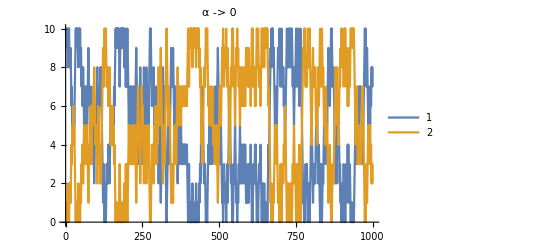

```mathematica
ListLinePlot[α0[[All,1;;1000]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"α -> 0"]
```

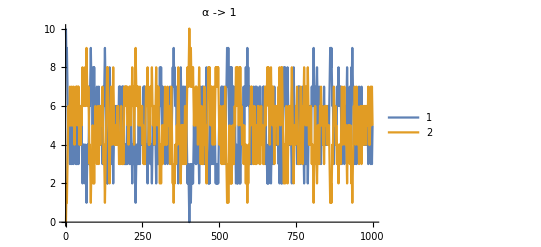

```mathematica
ListLinePlot[α1[[All,1;;1000]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"α -> 1"]
```

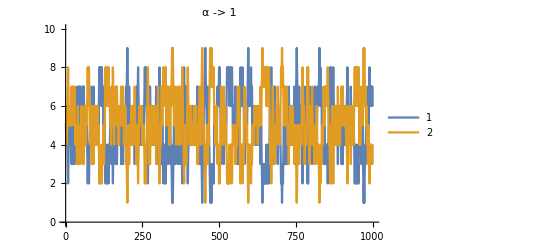

```mathematica
ListLinePlot[α1[[All,-1000;;-1]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"α -> 1"]
```

#### Averages (200 sims)

```mathematica
α=0;
lots0=Table[netEvolve[twonodes,1,1000NN],{200}];
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots0[[j]][[i]][[All,1]],{i,Length[lots0[[j]]]}]],{j,Length[lots0]}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,2}],{i,1,1000NN,100}];
```

```mathematica
Export[FileNameJoin[{"Data","lots0mdTwonodesallinone200sims.csv"}],lots0md];
```

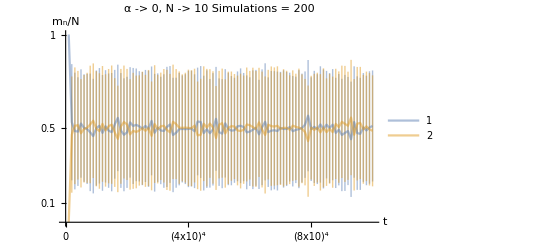

```mathematica
ListLinePlot[Transpose[lots0md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 0, N -> 10\nSimulations = 200",PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{Append[Prepend[Table[{i,Superscript[ToString[i/10]<>"x10",MantissaExponent[i][[2]]+1]},{i,20,80,20}],{0,0}],{100,Superscript[ToString[10]<>"x10",3]}],{0.1,0.5,1}}]
```

```mathematica
α=1;
lots1=Table[netEvolve[twonodes,1,1000 NN],{200}];
```

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,Length[lots1[[j]]]}]],{j,Length[lots1]}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,2}],{i,1,1000NN,100}];
```

```mathematica
Export[FileNameJoin[{"Data","lots1mdTwonodesallinone200sims.csv"}],lots1md];
```

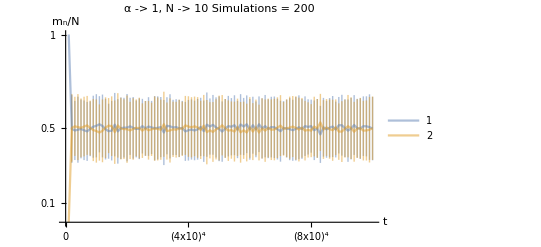

```mathematica
ListLinePlot[Transpose[lots1md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 1, N -> 10\nSimulations = 200",PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{Append[Prepend[Table[{i,Superscript[ToString[i/10]<>"x10",MantissaExponent[i][[2]]+1]},{i,20,80,20}],{0,0}],{100,Superscript[ToString[10]<>"x10",3]}],{0.1,0.5,1}}]
```

### 100 packages, distributed.

```mathematica
twonodes={{0,1},{1,0}};
```

```mathematica
M=Length[twonodes];
```

```mathematica
NN=100;
```

```mathematica
twonodes=graphToNet[AdjacencyGraph[twonodes],NN/2];
```

#### Averages (100 sims)

```mathematica
α=0;
time=10NN;
sims=100;
steps=20;
steppos=Position[Range[time]/NN,_Integer|Rational[_,2]|Rational[_,4]]//Flatten//Sort;
steppos=Prepend[steppos+1,1];
lots0=Table[netEvolve[twonodes,1,time],{sims}];
```

```mathematica
Position[Range[time]/NN,1]
```

{{100}}

```mathematica
steppos/NN
```

{1/4,1/2,3/4,1,5/4,3/2,7/4,2,9/4,5/2,11/4,3,13/4,7/2,15/4,4,17/4,9/2,19/4,5,21/4,11/2,23/4,6,25/4,13/2,27/4,7,29/4,15/2,31/4,8,33/4,17/2,35/4,9,37/4,19/2,39/4,10}

```mathematica
{{{0,0},}
```

```mathematica
steppos=Position[Range[time]/NN,_Integer|Rational[_,2]|Rational[_,4]]//Flatten//Sort;
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots0[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,M}],{i,1,time,steps}];
```

```mathematica
Export[FileNameJoin[{"Data","lots0mdTwonodesallinone100sims.csv"}],lots0md];
```

```mathematica
NN
```

100

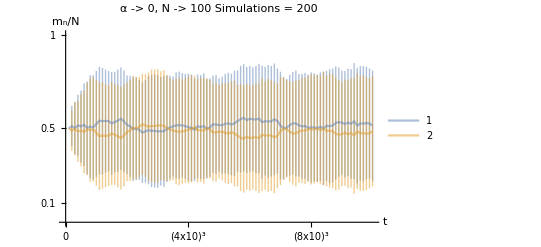

```mathematica
With[{thing=Transpose[lots0md],ticks={{{0,0},{Round[Length[thing[[1]]]/time 100],Superscript[ToString[1]<>"x10",2]},{Round[Length[thing[[1]]]/time 500],Superscript[ToString[5]<>"x10",2]},{Round[Length[thing[[1]]]/time 1000],Superscript[ToString[1]<>"x10",3]},{Length[thing[[1]]],Superscript[ToString[1.5]<>"x10",3]}},{0.1,0.5,1}}},
ListLinePlot[thing,PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> "<>ToString[α]<>", N -> "<>ToString[NN]<>"\nSimulations -> "<>ToString[sims],
PlotStyle->Opacity[0.5],AxesLabel->{"t/N","m_n/N"},Ticks->ticks]
]
```

```mathematica
α=1;
lots1=Table[netEvolve[twonodes,1,40NN],{100}];
```

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,Length[lots1[[j]]]}]],{j,Length[lots1]}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,2}],{i,1,40NN,50}];
```

```mathematica
Export[FileNameJoin[{"Data","lots1mdTwonodesallinone100sims.csv"}],lots1md];
```

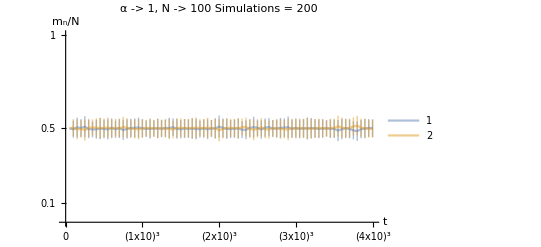

```mathematica
ListLinePlot[Transpose[lots1md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 1, N -> 100\nSimulations = 200",PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{20,("1x10")^3},{40,("2x10")^3},{60,("3x10")^3},{80,("4x10")^3}},{0.1,0.5,1}}]
```

## Directed triangle

```mathematica
triangle={{0,1,1},{1,0,0},{0,1,0}};
```

```mathematica
M=Length[triangle]
```

3

```mathematica
AdjacencyGraph[triangle]
```

-Graphics-

### 10 packages, all start in the same node

```mathematica
NN=10;
```

```mathematica
Δ=graphToNet[AdjacencyGraph[triangle],{NN,1}];
```

#### One sim

```mathematica
α=0;
tmp0=netEvolve[Δ,1,100 NN];
```

```mathematica
tmp0=Transpose[Table[Length/@tmp0[[i]][[All,1]],{i,Length[tmp0]}]];
```

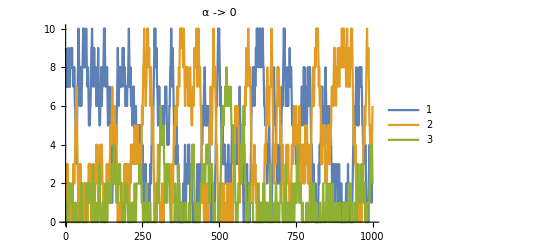

```mathematica
ListLinePlot[tmp0[[All,-1000;;-1]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"α -> 0"]
```

#### Averages (200 sims)

```mathematica
α=0;
lots=Table[netEvolve[Δ,1,1000 NN],{200}];
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots[[j]][[i]][[All,1]],{i,Length[lots[[j]]]}]],{j,Length[lots]}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,3}],{i,1,1000NN,100}];
```

```mathematica
Export[FileNameJoin[{"Data","lots0mdDirTriangleallinone200sims.csv"}],lots0md];
```

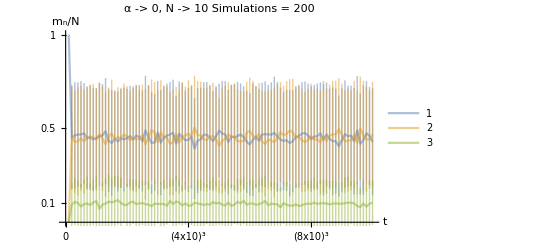

```mathematica
ListLinePlot[Transpose[lots0md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 0, N -> 10\nSimulations = 200",PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{Append[Prepend[Table[{i,Superscript[ToString[i/10]<>"x10",MantissaExponent[i][[2]]+1]},{i,20,80,20}],{0,0}],{100,Superscript[ToString[1]<>"x10",4]}],{0.1,0.5,1}}]
```

```mathematica
α=1;
lots1=Table[netEvolve[Δ,1,400 NN],{200}];
```

```mathematica
400NN
```

4000

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,Length[lots1[[j]]]}]],{j,Length[lots1]}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,3}],{i,1,400NN,50}];
```

```mathematica
Export[FileNameJoin[{"Data","lots1mdDirTriangleallinone200sims.csv"}],lots1md];
```

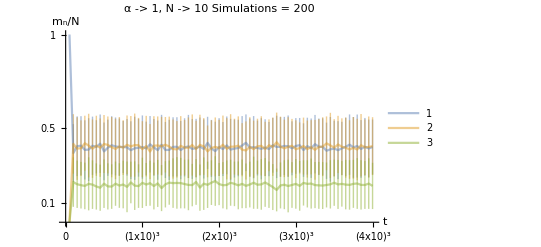

```mathematica
ListLinePlot[Transpose[lots1md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 1, N -> 10\nSimulations = 200",PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{20,("1x10")^3},{40,("2x10")^3},{60,("3x10")^3},{80,("4x10")^3}},{0.1,0.5,1}}]
```

### 100 packages, all start in the same node

```mathematica
NN=100;
```

```mathematica
Δ=graphToNet[AdjacencyGraph[triangle],{NN,1}];
```

#### Averages (200 sims)

```mathematica
α=0;
lots=Table[netEvolve[Δ,1,100 NN],{200}];
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots[[j]][[i]][[All,1]],{i,Length[lots[[j]]]}]],{j,Length[lots]}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,M}],{i,1,100NN,100}];
```

```mathematica
Export[FileNameJoin[{"Data","lots0mdDirTriangleall100inone200sims.csv"}],lots0md];
```

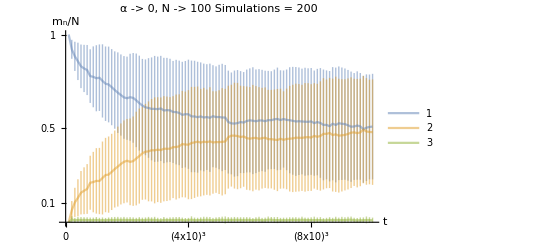

```mathematica
ListLinePlot[Transpose[lots0md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 0, N -> 100\nSimulations = 200",PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{Append[Prepend[Table[{i,Superscript[ToString[i/10]<>"x10",MantissaExponent[i][[2]]+1]},{i,20,80,20}],{0,0}],{100,Superscript[ToString[1]<>"x10",4]}],{0.1,0.5,1}}]
```

```mathematica
α=1;
lots1=Table[netEvolve[Δ,1,40 NN],{100}];
```

```mathematica
40NN
```

4000

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,Length[lots1[[j]]]}]],{j,Length[lots1]}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,3}],{i,1,40NN,50}];
```

```mathematica
Export[FileNameJoin[{"Data","lots1mdDirTriangleallinone100sims.csv"}],lots1md];
```

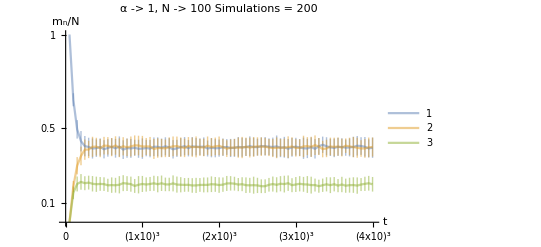

```mathematica
ListLinePlot[Transpose[lots1md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 1, N -> 100\nSimulations = 200",PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{20,("1x10")^3},{40,("2x10")^3},{60,("3x10")^3},{80,("4x10")^3}},{0.1,0.5,1}}]
```

### 99 packages, distributed.

```mathematica
NN=99;
```

```mathematica
Δ=graphToNet[AdjacencyGraph[triangle],NN/3];
```

#### Averages (100 sims)

```mathematica
α=0;
sims=100;
time=100NN;
lots0=Table[netEvolve[Δ,1,time],{sims}];
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots0[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,M}],{i,1,time,sims}];
```

```mathematica
Export[FileNameJoin[{"Data","lots0mdTriangleallinone100sims.csv"}],lots0md];
```

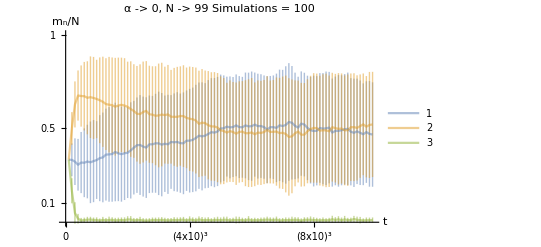

```mathematica
ListLinePlot[Transpose[lots0md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 0, N -> 99\nSimulations = 100",PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{Append[Prepend[Table[{i,Superscript[ToString[i/10]<>"x10",MantissaExponent[i][[2]]+1]},{i,20,80,20}],{0,0}],{100,Superscript[ToString[1]<>"x10",4]}],{0.1,0.5,1}}]
```

```mathematica
α=1;
lots1=Table[netEvolve[Δ,1,40 NN],{100}];
```

```mathematica
40NN
```

3960

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,Length[lots1[[j]]]}]],{j,Length[lots1]}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,3}],{i,1,40NN,50}];
```

```mathematica
Export[FileNameJoin[{"Data","lots1mdDirTriangleDistributed100sims.csv"}],lots1md];
```

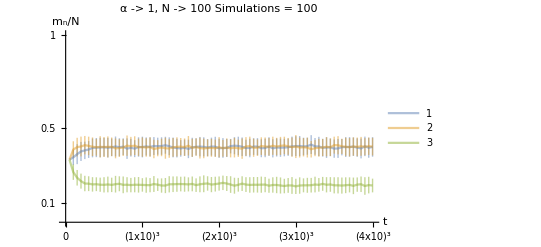

```mathematica
ListLinePlot[Transpose[lots1md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 1, N -> 100\nSimulations = 100",PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{20,("1x10")^3},{40,("2x10")^3},{60,("3x10")^3},{80,("4x10")^3}},{0.1,0.5,1}}]
```

## Non-directed triangle

```mathematica
ndtriangle={{0,1,1},{1,0,1},{1,1,0}};
```

```mathematica
M=Length[ndtriangle]
```

3

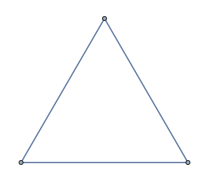

```mathematica
AdjacencyGraph[ndtriangle]
```

### 10 packages, all start in the same node

```mathematica
NN=10;
```

```mathematica
Δ=graphToNet[AdjacencyGraph[ndtriangle],{NN,1}];
```

#### One sim

```mathematica
α=0;
tmp0=netEvolve[Δ,1,1000 NN];
α=1;
tmp1=netEvolve[Δ,1,1000 NN];
```

```mathematica
tmp0=Transpose[Table[Length/@tmp0[[i]][[All,1]],{i,Length[tmp0]}]];
tmp1=Transpose[Table[Length/@tmp1[[i]][[All,1]],{i,Length[tmp1]}]];
```

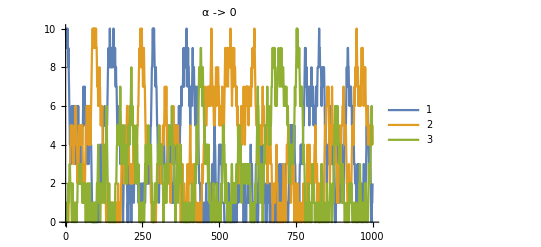

```mathematica
ListLinePlot[tmp0[[All,1;;1000]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"α -> 0"]
```

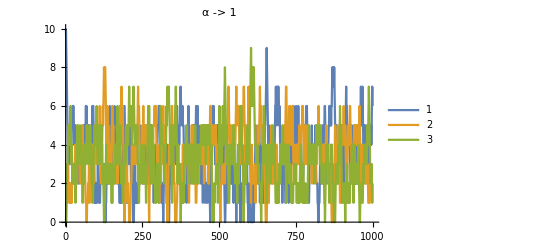

```mathematica
ListLinePlot[tmp1[[All,1;;1000]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"α -> 1"]
```

#### Averages (200 sims)

```mathematica
α=0;
lots=Table[netEvolve[Δ,1,1000 NN],{200}];
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots[[j]][[i]][[All,1]],{i,Length[lots[[j]]]}]],{j,Length[lots]}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,M}],{i,1,1000NN,100}];
```

```mathematica
Export[FileNameJoin[{"Data","lots0mdNDTriangleallinone200sims.csv"}],lots0md];
```

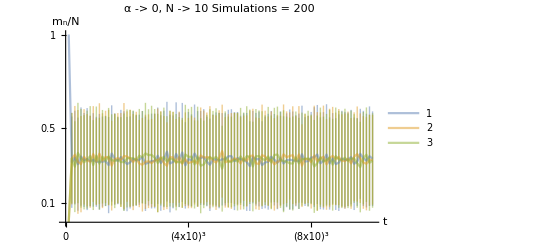

```mathematica
ListLinePlot[Transpose[lots0md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 0, N -> 10\nSimulations = 200",PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{Append[Prepend[Table[{i,Superscript[ToString[i/10]<>"x10",MantissaExponent[i][[2]]+1]},{i,20,80,20}],{0,0}],{100,Superscript[ToString[1]<>"x10",4]}],{0.1,0.5,1}}]
```

```mathematica
α=1;
time=400NN;
sims=200;
lots1=Table[netEvolve[Δ,1,time],{sims}];
```

```mathematica
time
```

4000

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,3}],{i,1,time,50}];
```

```mathematica
Export[FileNameJoin[{"Data","lots1mdNonDirTriangleallinone"<>ToString[sims]<>"sims.csv"}],lots1md];
```

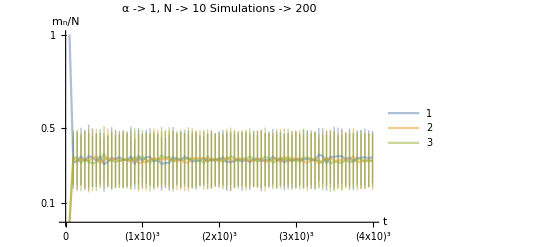

```mathematica
ListLinePlot[Transpose[lots1md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 1, N -> 10\nSimulations -> "<>ToString[sims],PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{20,("1x10")^3},{40,("2x10")^3},{60,("3x10")^3},{80,("4x10")^3}},{0.1,0.5,1}}]
```

### 100 packages, all start in the same node

```mathematica
NN=100;
sims=50;
time=150NN;
```

```mathematica
Δ=graphToNet[AdjacencyGraph[ndtriangle],{NN,1}];
```

#### Averages (50 sims)

```mathematica
α=0;
lots=Table[netEvolve[Δ,1,time],{sims}];
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,M}],{i,1,time,120}];
```

```mathematica
Export[FileNameJoin[{"Data","lots0mdNonDirTriangleall100inone"<>ToString[sims]<>"sims.csv"}],lots0md];
```

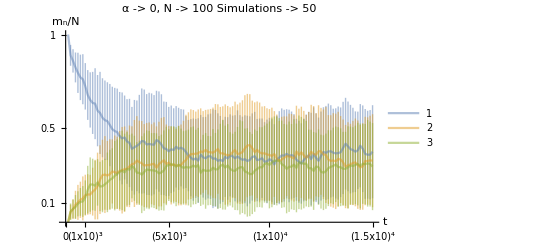

```mathematica
ListLinePlot[Transpose[lots0md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> 0, N -> 100\nSimulations -> "<>ToString[sims],PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{Round[Length[Transpose[lots0md][[1]]]/time 1000],Superscript[ToString[1]<>"x10",3]},{Round[Length[Transpose[lots0md][[1]]]/time 5000],Superscript[ToString[5]<>"x10",3]},{Round[Length[Transpose[lots0md][[1]]]/time 10000],Superscript[ToString[1]<>"x10",4]},{Length[Transpose[lots0md][[1]]],Superscript[ToString[1.5]<>"x10",4]}},{0.1,0.5,1}}]
```

```mathematica
α=1;
lots1=Table[netEvolve[Δ,1,time],{sims}];
```

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,M}],{i,1,time,120}];
```

```mathematica
Export[FileNameJoin[{"Data","lots"<>ToString[α]<>"mdNonDirTriangleall100inone"<>ToString[sims]<>"sims.csv"}],lots1md];
```

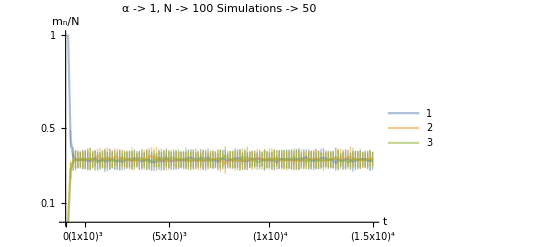

```mathematica
ListLinePlot[Transpose[lots1md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> "<>ToString[α]<>", N -> "<>ToString[NN]<>"\nSimulations -> "<>ToString[sims],PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{Round[Length[Transpose[lots1md][[1]]]/time 1000],Superscript[ToString[1]<>"x10",3]},{Round[Length[Transpose[lots1md][[1]]]/time 5000],Superscript[ToString[5]<>"x10",3]},{Round[Length[Transpose[lots1md][[1]]]/time 10000],Superscript[ToString[1]<>"x10",4]},{Length[Transpose[lots1md][[1]]],Superscript[ToString[1.5]<>"x10",4]}},{0.1,0.5,1}}]
```

### 99 packages, distributed.

```mathematica
Δ=graphToNet[AdjacencyGraph[ndtriangle],NN/3];
```

```mathematica
NN=99;
sims=50;
time=150NN;
```

#### Averages (50 sims)

```mathematica
α=0;
lots0=Table[netEvolve[Δ,1,time],{sims}];
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots0[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,M}],{i,1,time,120}];
```

```mathematica
Export[FileNameJoin[{"Data","lots"<>ToString[α]<>"mdNonDirTriangle"<>ToString[NN]<>"distributed"<>ToString[sims]<>"sims.csv"}],lots0md];
```

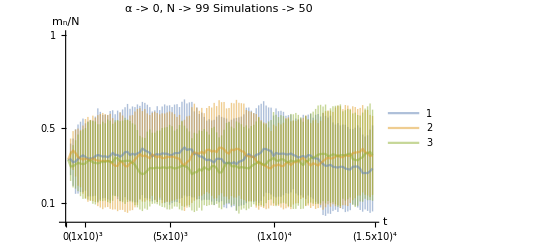

```mathematica
ListLinePlot[Transpose[lots0md],PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> "<>ToString[α]<>", N -> "<>ToString[NN]<>"\nSimulations -> "<>ToString[sims],
PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{Round[Length[Transpose[lots1md][[1]]]/time 1000],Superscript[ToString[1]<>"x10",3]},{Round[Length[Transpose[lots1md][[1]]]/time 5000],Superscript[ToString[5]<>"x10",3]},{Round[Length[Transpose[lots1md][[1]]]/time 10000],Superscript[ToString[1]<>"x10",4]},{Length[Transpose[lots1md][[1]]],Superscript[ToString[1.5]<>"x10",4]}},{0.1,0.5,1}}]
```

```mathematica
α=1;
lots1=Table[netEvolve[Δ,1,time],{sims}];
```

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,M}],{i,1,time,120}];
```

```mathematica
Export[FileNameJoin[{"Data","lots"<>ToString[α]<>"mdNonDirTriangle"<>ToString[NN]<>"distributed"<>ToString[sims]<>"sims.csv"}],lots0md];
```

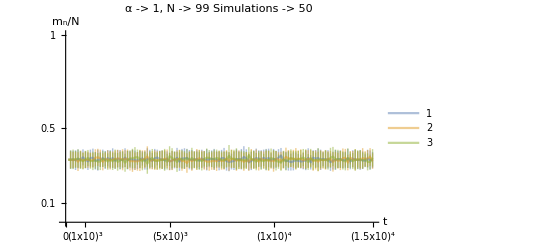

```mathematica
With[{thing=Transpose[lots1md]},
ListLinePlot[thing,PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> "<>ToString[α]<>", N -> "<>ToString[NN]<>"\nSimulations -> "<>ToString[sims],
PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{Round[Length[thing[[1]]]/time 1000],Superscript[ToString[1]<>"x10",3]},{Round[Length[thing[[1]]]/time 5000],Superscript[ToString[5]<>"x10",3]},{Round[Length[thing[[1]]]/time 10000],Superscript[ToString[1]<>"x10",4]},{Length[thing[[1]]],Superscript[ToString[1.5]<>"x10",4]}},{0.1,0.5,1}}]
]
```

## 5 nodes

```mathematica
five={{0,1,0,0,0},{1,0,1,1,0},{0,1,0,1,0},{0,1,1,0,1},{0,0,0,1,0}};
```

```mathematica
M=Length[five]
```

5

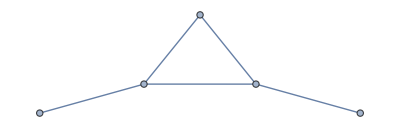

```mathematica
AdjacencyGraph[five]
```

### 10 packages, all start in the same node

```mathematica
NN=10;
```

```mathematica
five=graphToNet[AdjacencyGraph[five],{NN,5}];
```

#### One sim

```mathematica
α=0;
tmp0=netEvolve[five,1,1000 NN];
α=1;
tmp1=netEvolve[five,1,1000 NN];
```

```mathematica
tmp0=Transpose[Table[Length/@tmp0[[i]][[All,1]],{i,Length[tmp0]}]];
tmp1=Transpose[Table[Length/@tmp1[[i]][[All,1]],{i,Length[tmp1]}]];
```

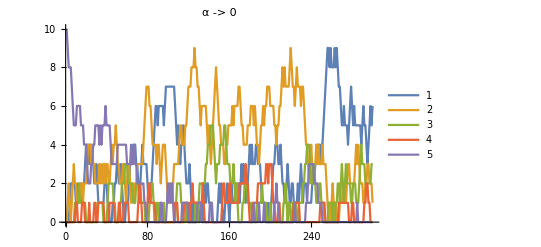

```mathematica
ListLinePlot[tmp0[[All,1;;300]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"α -> 0"]
```

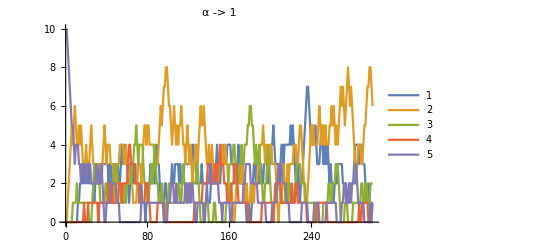

```mathematica
ListLinePlot[tmp1[[All,1;;300]],PlotLegends->Automatic,PlotRange->{0,NN},PlotLabel->"α -> 1"]
```

#### Averages (100 sims)

```mathematica
sims=100;
time=150NN;
```

```mathematica
α=0;
lots0=Table[netEvolve[five,1,time],{sims}];
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots0[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,M}],{i,1,time,20}];
```

```mathematica
Export[FileNameJoin[{"Data","lots"<>ToString[α]<>"mdFive"<>ToString[NN]<>"allinone"<>ToString[sims]<>"sims.csv"}],lots0md];
```

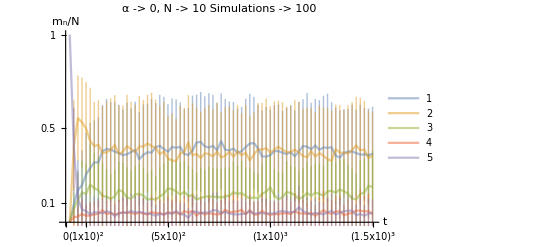

```mathematica
With[{thing=Transpose[lots0md]},
ListLinePlot[thing,PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> "<>ToString[α]<>", N -> "<>ToString[NN]<>"\nSimulations -> "<>ToString[sims],
PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{Round[Length[thing[[1]]]/time 100],Superscript[ToString[1]<>"x10",2]},{Round[Length[thing[[1]]]/time 500],Superscript[ToString[5]<>"x10",2]},{Round[Length[thing[[1]]]/time 1000],Superscript[ToString[1]<>"x10",3]},{Length[thing[[1]]],Superscript[ToString[1.5]<>"x10",3]}},{0.1,0.5,1}}]
]
```

```mathematica
α=1;
time=150NN;
sims=100;
lots1=Table[netEvolve[five,1,time],{sims}];
```

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,M}],{i,1,time,20}];
```

```mathematica
Export[FileNameJoin[{"Data","lots"<>ToString[α]<>"mdFive"<>ToString[NN]<>"allinone"<>ToString[sims]<>"sims.csv"}],lots1md];
```

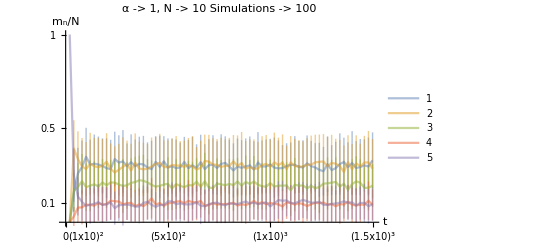

```mathematica
With[{thing=Transpose[lots1md]},
ListLinePlot[thing,PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> "<>ToString[α]<>", N -> "<>ToString[NN]<>"\nSimulations -> "<>ToString[sims],
PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{Round[Length[thing[[1]]]/time 100],Superscript[ToString[1]<>"x10",2]},{Round[Length[thing[[1]]]/time 500],Superscript[ToString[5]<>"x10",2]},{Round[Length[thing[[1]]]/time 1000],Superscript[ToString[1]<>"x10",3]},{Length[thing[[1]]],Superscript[ToString[1.5]<>"x10",3]}},{0.1,0.5,1}}]
]
```

### 100 packages, all start in the same node

```mathematica
NN=100;
```

```mathematica
five=graphToNet[AdjacencyGraph[five],{NN,1}];
```

#### Averages (50 sims)

```mathematica
sims=50;
time=150NN;
```

```mathematica
α=0;
lots0=Table[netEvolve[five,1,time],{sims}];
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots0[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,M}],{i,1,time,20}];
```

```mathematica
Export[FileNameJoin[{"Data","lots"<>ToString[α]<>"mdFive"<>ToString[NN]<>"allinone"<>ToString[sims]<>"sims.csv"}],lots0md];
```

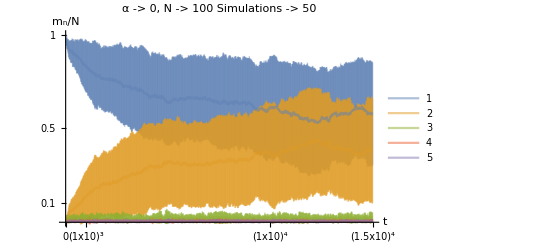

```mathematica
With[{thing=Transpose[lots0md],step=20},
ListLinePlot[thing,PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> "<>ToString[α]<>", N -> "<>ToString[NN]<>"\nSimulations -> "<>ToString[sims],
PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{1000/step,Superscript[ToString[1]<>"x10",3]},{10000/step,Superscript[ToString[1]<>"x10",4]},{Length[thing[[1]]],Superscript[ToString[1.5]<>"x10",4]}},{0.1,0.5,1}}]
]
```

```mathematica
α=1;
time=150NN;
sims=50;
lots1=Table[netEvolve[five,1,time],{sims}];
```

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,M}],{i,1,time,20}];
```

```mathematica
Export[FileNameJoin[{"Data","lots"<>ToString[α]<>"mdFive"<>ToString[NN]<>"allinone"<>ToString[sims]<>"sims.csv"}],lots1md];
```

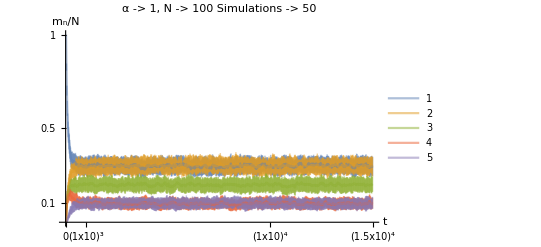

```mathematica
With[{thing=Transpose[lots1md],step=20},
ListLinePlot[thing,PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> "<>ToString[α]<>", N -> "<>ToString[NN]<>"\nSimulations -> "<>ToString[sims],
PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{1000/step,Superscript[ToString[1]<>"x10",3]},{10000/step,Superscript[ToString[1]<>"x10",4]},{Length[thing[[1]]],Superscript[ToString[1.5]<>"x10",4]}},{0.1,0.5,1}}]
]
```

### 100 packages, distributed.

```mathematica
five={{0,1,0,0,0},{1,0,1,1,0},{0,1,0,1,0},{0,1,1,0,1},{0,0,0,1,0}};
```

```mathematica
five=graphToNet[AdjacencyGraph[five],NN/5];
```

```mathematica
sims=50;
time=150NN;
```

#### Averages (50 sims)

```mathematica
α=0;
lots0=Table[netEvolve[five,1,time],{sims}];
```

```mathematica
lots0=Table[Transpose[Table[1./NN Length/@lots0[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots0md=Table[Table[Around[Transpose[lots0[[All,n]]][[i]]],{n,M}],{i,1,time,120}];
```

```mathematica
Export[FileNameJoin[{"Data","lots"<>ToString[α]<>"mdNonDirTriangle"<>ToString[NN]<>"distributed"<>ToString[sims]<>"sims.csv"}],lots0md];
```

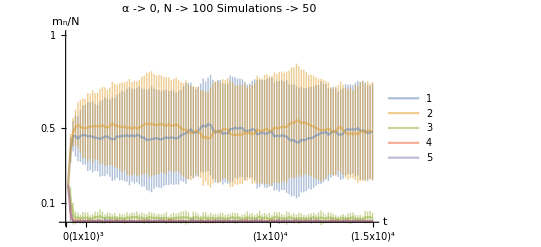

```mathematica
With[{thing=Transpose[lots0md],step=120},
ListLinePlot[thing,PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> "<>ToString[α]<>", N -> "<>ToString[NN]<>"\nSimulations -> "<>ToString[sims],
PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{1000/step,Superscript[ToString[1]<>"x10",3]},{10000/step,Superscript[ToString[1]<>"x10",4]},{Length[thing[[1]]],Superscript[ToString[1.5]<>"x10",4]}},{0.1,0.5,1}}]
]
```

```mathematica
α=1;
lots1=Table[netEvolve[five,1,time],{sims}];
```

```mathematica
lots1=Table[Transpose[Table[1./NN Length/@lots1[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
```

```mathematica
lots1md=Table[Table[Around[Transpose[lots1[[All,n]]][[i]]],{n,M}],{i,1,time,120}];
```

```mathematica
Export[FileNameJoin[{"Data","lots"<>ToString[α]<>"mdNonDirTriangle"<>ToString[NN]<>"distributed"<>ToString[sims]<>"sims.csv"}],lots0md];
```

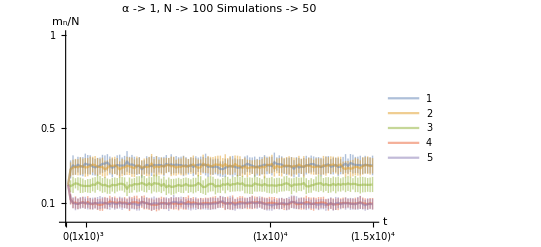

```mathematica
With[{thing=Transpose[lots1md],step=120},
ListLinePlot[thing,PlotLegends->Automatic,PlotRange->{0,1},PlotLabel->"α -> "<>ToString[α]<>", N -> "<>ToString[NN]<>"\nSimulations -> "<>ToString[sims],
PlotStyle->Opacity[0.5],AxesLabel->{"t","m_n/N"},Ticks->{{{0,0},{1000/step,Superscript[ToString[1]<>"x10",3]},{10000/step,Superscript[ToString[1]<>"x10",4]},{Length[thing[[1]]],Superscript[ToString[1.5]<>"x10",4]}},{0.1,0.5,1}}]
]
```

## All networks, <spread> Vs. α for all nodes

## 2 nodes

```mathematica
twonodes={{0,1},{1,0}};
```

```mathematica
M=Length[twonodes];
time=100;
sims=200;
```

```mathematica
twonodes=graphToNet[AdjacencyGraph[twonodes],5];
```

```mathematica
For[α=0;αspread=ConstantArray[{},M],α<=1,α+=0.1,
lots=Table[netEvolve[twonodes,1,time],{sims}];
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,M}],{i,time+1}];
For[i=1,i<=M,i++,
AppendTo[αspread[[i]],{α,Around[spread[#]&/@lotsmd[[All,i]][[-50;;-1]]]}]
];
];
For[α=1,α<=10,α++,
lots=Table[netEvolve[twonodes,1,time],{sims}];
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,M}],{i,time+1}];
For[i=1,i<=M,i++,
AppendTo[αspread[[i]],{α,Around[spread[#]&/@lotsmd[[All,i]][[-50;;-1]]]}]
];
];
```

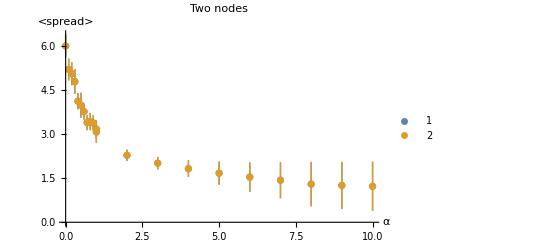

```mathematica
ListPlot[αspread,AxesLabel->{"α","<spread>"},PlotLabel->"Two nodes",PlotLegends->Automatic]
```

## Directed triangle

```mathematica
triangle={{0,1,1},{1,0,0},{0,1,0}};
```

```mathematica
M=Length[triangle];
time=100;
sims=200;
```

```mathematica
triangle=graphToNet[AdjacencyGraph[triangle],{{1,2,3,4},{5,6,7,8},{9,10}}];
```

```mathematica
For[α=0;αspread=ConstantArray[{},M],α<=1,α+=0.1,
lots=Table[netEvolve[triangle,1,time],{sims}];
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,M}],{i,time+1}];
For[i=1,i<=M,i++,
AppendTo[αspread[[i]],{α,Around[spread[#]&/@lotsmd[[All,i]][[-50;;-1]]]}]
];
];
For[α=1,α<=10,α++,
lots=Table[netEvolve[triangle,1,time],{sims}];
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,M}],{i,time+1}];
For[i=1,i<=M,i++,
AppendTo[αspread[[i]],{α,Around[spread[#]&/@lotsmd[[All,i]][[-50;;-1]]]}]
];
];
```

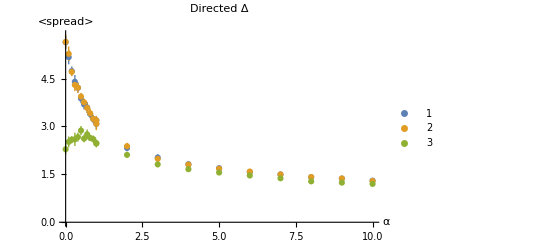

```mathematica
ListPlot[αspread,AxesLabel->{"α","<spread>"},PlotLabel->"Directed Δ",PlotLegends->Automatic]
```

## Non-directed triangle

```mathematica
ndtriangle={{0,1,1},{1,0,1},{1,1,0}};
```

```mathematica
M=Length[ndtriangle];
time=100;
sims=200;
```

```mathematica
ndtriangle=graphToNet[AdjacencyGraph[ndtriangle],{{1,2,3},{5,6,7},{8,9,10}}];
```

```mathematica
For[α=0;αspread=ConstantArray[{},M],α<=1,α+=0.1,
lots=Table[netEvolve[ndtriangle,1,time],{sims}];
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,M}],{i,time+1}];
For[i=1,i<=M,i++,
AppendTo[αspread[[i]],{α,Around[spread[#]&/@lotsmd[[All,i]][[-50;;-1]]]}]
];
];
For[α=1,α<=10,α++,
lots=Table[netEvolve[ndtriangle,1,time],{sims}];
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,M}],{i,time+1}];
For[i=1,i<=M,i++,
AppendTo[αspread[[i]],{α,Around[spread[#]&/@lotsmd[[All,i]][[-50;;-1]]]}]
];
];
```

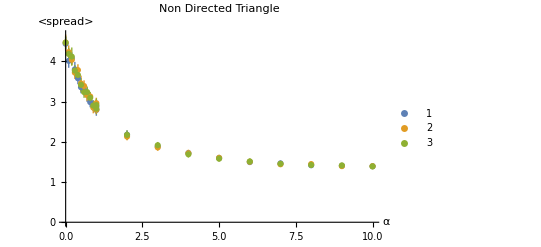

```mathematica
ListPlot[αspread,AxesLabel->{"α","<spread>"},PlotLabel->"Non Directed\n Triangle",PlotLegends->Automatic]
```

## 5 nodes

```mathematica
five={{0,1,0,0,0},{1,0,1,1,0},{0,1,0,1,0},{0,1,1,0,1},{0,0,0,1,0}};
```

```mathematica
M=Length[five];
time=100;
sims=100;
```

```mathematica
five=graphToNet[AdjacencyGraph[five],{{1,2,3},{4,5,6},{7,8},{9},{10}}];
```

```mathematica
For[α=0;αspread=ConstantArray[{},M],α<=1,α+=0.1,
lots=Table[netEvolve[five,1,time],{sims}];
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,M}],{i,time+1}];
For[i=1,i<=M,i++,
AppendTo[αspread[[i]],{α,Around[spread[#]&/@lotsmd[[All,i]][[-50;;-1]]]}]
];
];
For[α=1,α<=10,α++,
lots=Table[netEvolve[five,1,time],{sims}];
lots=Table[Transpose[Table[Length/@lots[[j]][[i]][[All,1]],{i,time+1}]],{j,sims}];
lotsmd=Table[Table[Around[Transpose[lots[[All,n]]][[i]]],{n,M}],{i,time+1}];
For[i=1,i<=M,i++,
AppendTo[αspread[[i]],{α,Around[spread[#]&/@lotsmd[[All,i]][[-50;;-1]]]}]
];
];
```

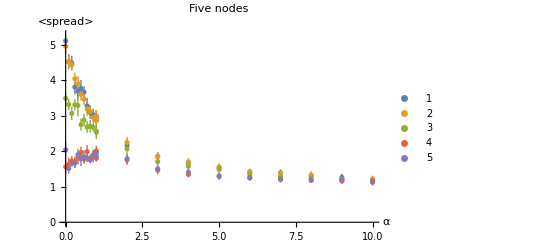

```mathematica
ListPlot[αspread,AxesLabel->{"α","<spread>"},PlotLabel->"Five nodes",PlotLegends->Automatic]
```